Histogram::hbins: The bin specification Probability cannot be used to determine either how many or which bins to use.

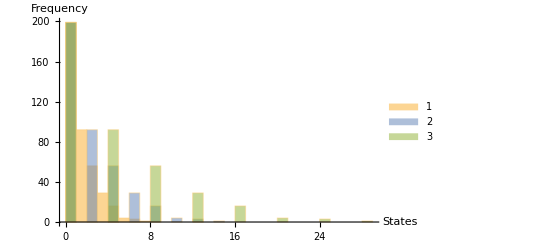

No. of Sites: 400

No. of iterations: 400

175

```mathematica
For[datalist1=Table[(1^n),{n,1,400}];datalist2=Table[(1^n)+1,{n,1,400}];datalist3=Table[(1^n)+3,{n,1,400}];p=1,p≤400,p++,

removesite=RandomInteger[{1,400}];
addsite=RandomInteger[{1,400}];

datalist1[[addsite]]=datalist1[[addsite]]+datalist1[[removesite]];
datalist1[[removesite]]=0;

datalist2[[addsite]]=datalist2[[addsite]]+datalist2[[removesite]];
datalist2[[removesite]]=0;

datalist3[[addsite]]=datalist3[[addsite]]+datalist3[[removesite]];
datalist3[[removesite]]=0;

]
Histogram[{datalist1,datalist2,datalist3},"Probability",AxesLabel->{"States","Frequency"},ChartLegends->{"Initial Quanta per site = 1","Initial Quanta per site = 2","Initial Quanta per site = 3"}]
Print["No. of Sites: 400"]
Print["No. of iterations: 400"]
```